# Final Lab Report

Edwin Marcelo Vasconez Lopez
School of Physical Sciences and Nanotechnology, Yachay Tech University, Urcuqui, Ecuador

## Part III. The Silicon atom

```mathematica
data1=Import["/home/edwin/wrk/DFT/Lab1/part1/cell1.dat","Table"];
data2=Import["/home/edwin/wrk/DFT/Lab1/part1/cell2.dat","Table"];
```

```mathematica
{data1,data2}//ListLinePlot[#,
Mesh->Full,PlotMarkers->{Automatic, 8}, Frame->True,PlotTheme->"Scientific",
Axes->None,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
FrameStyle->Black,
FrameLabel->{"Cell Length (Å)","Energy (eV)"}, ImageSize->400,
PlotStyle->{{Red,Thick},{Blue,Thick}},InterpolationOrder->2,Epilog->{Inset[Panel[Grid[{{"●","■"},{"ISPIN=1","ISPIN=2"}}//Transpose//Map[Style[#,18]&,#,{2}]&]],{Right,Top},{1.2,1.3}]}]&
```

-Graphics-

The blue line represents the result of a calculation considering the spin polarization of a Si atom. Also, the total energy is lower than the energy value computed neglecting polarization. Thus, the most stable state is when the isolated Si is magnetic.

## Part IV. The Chloride ion

```mathematica
data1a=Import["/home/edwin/wrk/DFT/Lab1/part2/cellold.dat","Table"];
data2a=Import["/home/edwin/wrk/DFT/Lab1/part2/cell.dat","Table"];
```

```mathematica
{data1a,data2a}//ListLinePlot[#,
Mesh->Full,PlotMarkers->{Automatic, 8}, Frame->True,PlotTheme->"Scientific",
Axes->None,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
FrameStyle->Black,
FrameLabel->{"Cell Length (Å)","Energy (eV)"}, ImageSize->400,
PlotStyle->{{Red,Thick},{Blue,Thick}},InterpolationOrder->1,Epilog->{Inset[Panel[Grid[{{"●","■"},{"No IDIPOL","IDIPOL=4"}}//Transpose//Map[Style[#,18]&,#,{2}]&]],{Right,Top},{1.2,1.3}]}]&
```

-Graphics-

First, if we use IDIPOL=4 the full dipole moment in all directions will be calculated. The first thing that we can see is that there is not convergency with no IDIPOL. Then the most stable configuration for the Chloride ion is that one in which we consider dipole-dipole corrections.

## Part V. The Silicon Crystal

```mathematica
dataecut=Import["/home/edwin/wrk/DFT/Lab2/part3_silicon/ecut.dat","Table"];
datakpt=Import["/home/edwin/wrk/DFT/Lab2/part3_silicon/kps.dat","Table"]//Map[#/{1,2}&,#]&
datacell=Import["/home/edwin/wrk/DFT/Lab2/part3_silicon/cell.dat","Table"];
```

{{3,-5.13186},{4,-5.34158},{5,-5.4016},{6,-5.42124},{7,-5.42824},{8,-5.43091},{9,-5.43198},{10,-5.43244},{11,-5.43262},{12,-5.43272}}

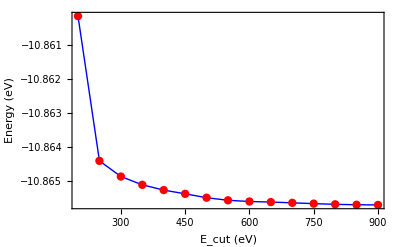

```mathematica
{dataecut}//ListLinePlot[#,
Mesh->Full,PlotMarkers->{Automatic,0}, Frame->True,PlotTheme->"Scientific",
Axes->None,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},FrameStyle->Black,
FrameLabel->{"E_cut (eV)","Energy (eV)"}, ImageSize->400,PlotRange->All,
PlotStyle->{{Blue,Thick},{Blue,Thick}},Epilog->{Red,AbsolutePointSize[6],Point[dataecut]}](*Epilog->{Inset[Panel[Grid[{{"●","■"},{"ISPIN=1","ISPIN=2"}}//Transpose//Map[Style[#,18]&,#,{2}]&]],{Right,Top},{1.2,1.3}]}]*)&
```

The blue line represents the result of a calculation considering the spin polarization of a Si atom. Also, the total energy is lower than the energy value computed neglecting polarization. Thus, the most stable state is when the isolated Si is magnetic. Here we are find the convergency of the E_cut.

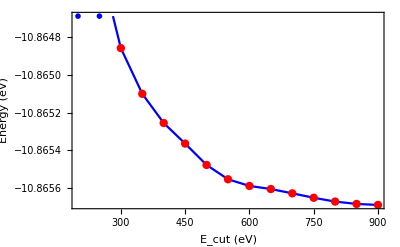

```mathematica
{dataecut}//ListLinePlot[#,
Mesh->Full,PlotMarkers->{Automatic,0}, Frame->True,PlotTheme->"Scientific",
Axes->None,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},FrameStyle->Black,
FrameLabel->{"E_cut (eV)","Energy (eV)"}, ImageSize->400,PlotRange->{-10.86568862+ 10^-3,-10.86568862},
PlotStyle->{Blue,Thick},Epilog->{Red,AbsolutePointSize[6],Point[dataecut]}](*Epilog->{Inset[Panel[Grid[{{"●","■"},{"ISPIN=1","ISPIN=2"}}//Transpose//Map[Style[#,18]&,#,{2}]&]],{Right,Top},{1.2,1.3}]}]*)&
```

As we can see in the figure we found the value of E_cut=300eV for a convergency  < 1meV. In addition, the cutoff energy tells us about the cutoff on the number of plane wave functions being utilized as basis functions to represent the wavefunction. Theoretically, an infinite number of basis functions is required to produce an exact answer. However, this is not computationally feasible and a cutoff must be introduced.

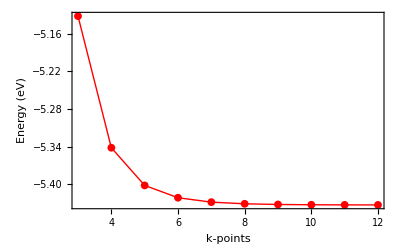

```mathematica
{datakpt}//ListLinePlot[#,
Mesh->Full,PlotMarkers->{Automatic, 8}, Frame->True,PlotTheme->"Scientific",PlotRange->All,
Axes->None,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},FrameStyle->Black,
FrameLabel->{"k-points","Energy (eV)"}, ImageSize->400,
PlotStyle->{{Red,Thick},{Blue,Thick}}](*Epilog->{Inset[Panel[Grid[{{"●","■"},{"ISPIN=1","ISPIN=2"}}//Transpose//Map[Style[#,18]&,#,{2}]&]],{Right,Top},{1.2,1.3}]}]*)&
```

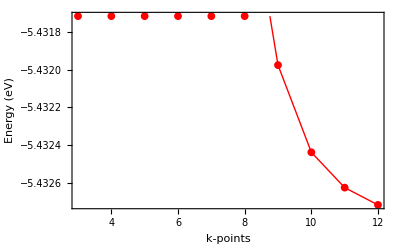

```mathematica
{datakpt}//ListLinePlot[#,
Mesh->Full,PlotMarkers->{Automatic, 8}, Frame->True,PlotTheme->"Scientific",PlotRange->{-5.431716065,-5.432716065},
Axes->None,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},FrameStyle->Black,
FrameLabel->{"k-points","Energy (eV)"}, ImageSize->400,
PlotStyle->{{Red,Thick},{Blue,Thick}},InterpolationOrder->1](*Epilog->{Inset[Panel[Grid[{{"●","■"},{"ISPIN=1","ISPIN=2"}}//Transpose//Map[Style[#,18]&,#,{2}]&]],{Right,Top},{1.2,1.3}]}]*)&
```

As we can see in the figure we found the value of k-points=[9x 9 x 9] for a convergency  < 1meV.

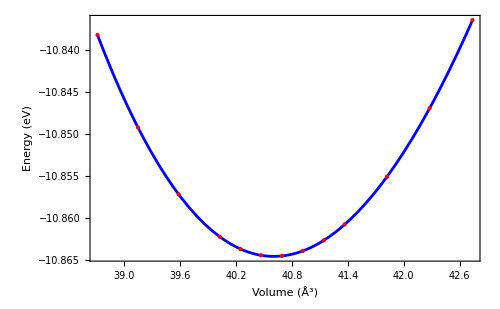

```mathematica
volData=(datacell[[1;;-1,1;;2]]//Transpose)^{3,1} {0.25,1}//Transpose;
EqState=c1+c2 x^-2+c3 x^(-4/3)+c4 x^(-2/3);
FitEqState=EqState/.FindFit[volData,EqState,{c1,c2,c3,c4},x ];
Vol=volData//Transpose//#[[1]]&;
Plot[FitEqState ,{x, Vol//Min, Vol//Max}, ImageSize->500,
Frame->True,PlotTheme->"Scientific",Axes->None,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},FrameStyle->Black,
PlotStyle->{Blue,{AbsoluteThickness[2]}}, Epilog->{PointSize[Large],Red,volData//Map[Point[#]&,#]&}, FrameLabel->{"Volume  (Å^3)", "Energy  (eV)"},
Axes->None]
```

```mathematica
VolOptim=FindMinimum[FitEqState,{x,40.5}]
<<Units`
x D[FitEqState,{x,2}]/.VolOptim[[2]]//Convert[# ElectronVolt/(10^-10 Meter)^3,Giga Pascal]&
(x/0.25)^(1/3)/.VolOptim[[2]]
```

{-10.8646,{x→40.6057}}

88.0439 Giga Pascal

5.4561

## Part VI. Silicon Crystal Functionals and Potentials

```mathematica
datacellda=Import["/home/edwin/wrk/DFT/Lab2/part4_silicon2/cell-lda.dat","Table"];
datacelpbe=Import["/home/edwin/wrk/DFT/Lab2/part4_silicon2/cell-pbe.dat","Table"];
```

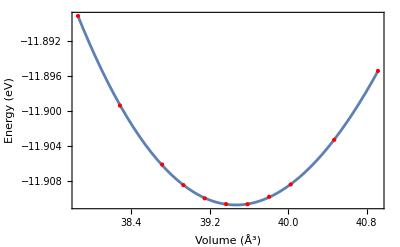

```mathematica
volData=(datacellda[[1;;-1,1;;2]]//Transpose)^{3,1} {0.25,1}//Transpose;(*0.25*)
EqState=c1+c2 x^-2+c3 x^(-4/3)+c4 x^(-2/3);
FitEqState=EqState/.FindFit[volData,EqState,{c1,c2,c3,c4},x ];
Vol=volData//Transpose//#[[1]]&;
Plot[FitEqState ,{x, Vol//Min, Vol//Max}, 
Frame->True,
PlotStyle->{{AbsoluteThickness[2]}}, Epilog->{PointSize[Large],Red,volData//Map[Point[#]&,#]&}, FrameLabel->{"Volume  (Å^3)", "Energy  (eV)"},
Axes->None]
```

```mathematica
VolOptim=FindMinimum[FitEqState,{x,40.5}]
<<Units`
x D[FitEqState,{x,2}]/.VolOptim[[2]]//Convert[# ElectronVolt/(10^-10 Meter)^3,Giga Pascal]&
(x/0.25)^(1/3)/.VolOptim[[2]]
```

{-11.9107,{x→39.4667}}

97.8002 Giga Pascal

5.4046

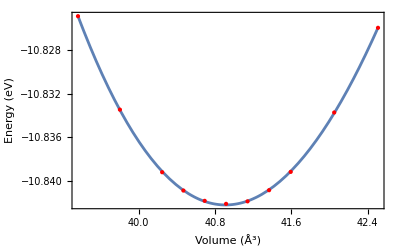

```mathematica
volData=(datacelpbe[[1;;-1,1;;2]]//Transpose)^{3,1} {0.25,1}//Transpose;(*0.25*)
EqState=c1+c2 x^-2+c3 x^(-4/3)+c4 x^(-2/3);
FitEqState=EqState/.FindFit[volData,EqState,{c1,c2,c3,c4},x ];
Vol=volData//Transpose//#[[1]]&;
Plot[FitEqState ,{x, Vol//Min, Vol//Max}, 
Frame->True,
PlotStyle->{{AbsoluteThickness[2]}}, Epilog->{PointSize[Large],Red,volData//Map[Point[#]&,#]&}, FrameLabel->{"Volume  (Å^3)", "Energy  (eV)"},
Axes->None]
```

```mathematica
VolOptim=FindMinimum[FitEqState,{x,40.5}]
<<Units`
x D[FitEqState,{x,2}]/.VolOptim[[2]]//Convert[# ElectronVolt/(10^-10 Meter)^3,Giga Pascal]&
(x/0.25)^(1/3)/.VolOptim[[2]]
```

{-10.8422,{x→40.9104}}

89.4629 Giga Pascal

5.46971

## Part VII. The Silicon Crystal - Ground State Properties

```mathematica
Nn=2;
Subscript[E, sin]=-0.88361994;Subscript[E, bulk]=-10.84206825;
Subscript[E, co]=-Subscript[E, sin]+Subscript[E, bulk]/Nn
```

-4.53741

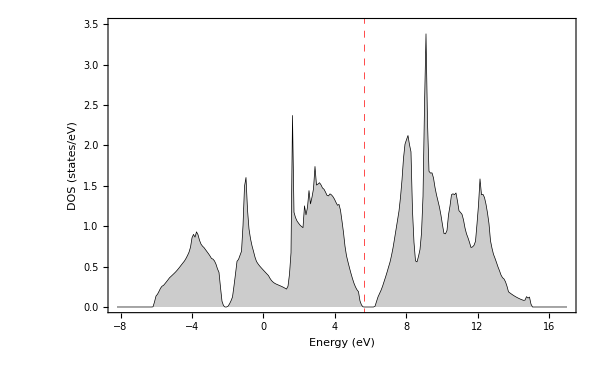

```mathematica
datados=Import["/home/edwin/wrk/DFT/Lab3/part5_silicon3/DOSCAR","Table"][[7;;7+300]][[All,{1,2}]];
efer=Import["/home/edwin/wrk/DFT/Lab3/part5_silicon3/DOSCAR","Table"][[6,4]];
ListPlot[datados,
Joined->True,
Frame->True,
Axes->False,
GridLines->{{efer},None},
GridLinesStyle->Directive[Red, Dashed],
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
Filling->Axis,
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->600,
PlotRange->{All,{0,3.5}}
]
```

## Part VIII. The Silicon Crystal Faces

```mathematica
Import["/home/edwin/wrk/DFT/Lab3/CHGCAR.png"]
```

-Graphics-

### E-cut

{{250,-5.11849},{300,-5.12533},{350,-5.12891},{400,-5.13028},{450,-5.13053},{500,-5.13057},{550,-5.13061},{600,-5.13067},{650,-5.13069},{700,-5.13069},{750,-5.13068},{800,-5.13067},{900,-5.13068},{850,-5.13067}}

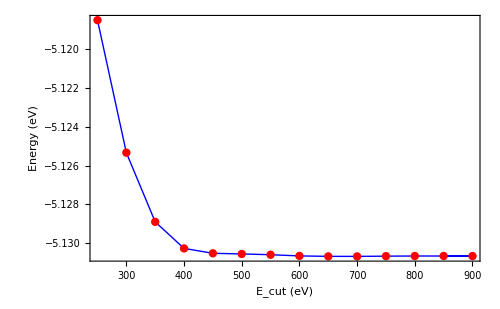

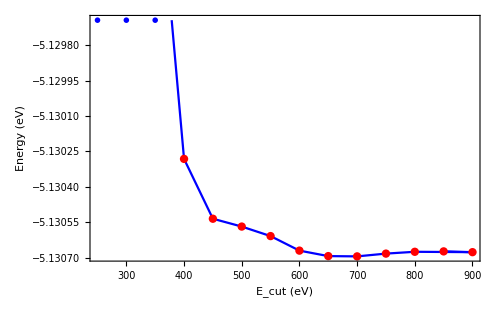

```mathematica
dataecut=Import["/home/edwin/wrk/DFT/part6/results/ecut.dat","Table"]//Map[#/{1,2}&,#]&(*Number of atoms /2*)
{dataecut}//ListLinePlot[#,
Mesh->Full,PlotMarkers->{Automatic,0}, Frame->True,PlotTheme->"Scientific",
Axes->None,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},FrameStyle->Black,
FrameLabel->{"E_cut (eV)","Energy (eV)"}, ImageSize->500,PlotRange->All,
PlotStyle->{{Blue,Thick},{Blue,Thick}},Epilog->{Red,AbsolutePointSize[6],Point[dataecut]}]&
{dataecut}//ListLinePlot[#,
Mesh->Full,PlotMarkers->{Automatic,0}, Frame->True,PlotTheme->"Scientific",
Axes->None,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},FrameStyle->Black,
FrameLabel->{"E_cut (eV)","Energy (eV)"}, ImageSize->500,PlotRange->{-5.13069423+10^-3,-5.13069423},
PlotStyle->{Blue,Thick},Epilog->{Red,AbsolutePointSize[6],Point[dataecut]}]&
```

### K-points

{{8,-5.13042},{9,-5.13029},{10,-5.13452},{11,-5.13425},{12,-5.13512},{13,-5.13391},{14,-5.13295},{15,-5.13388},{16,-5.13376},{17,-5.13333},{18,-5.13367},{19,-5.13346}}

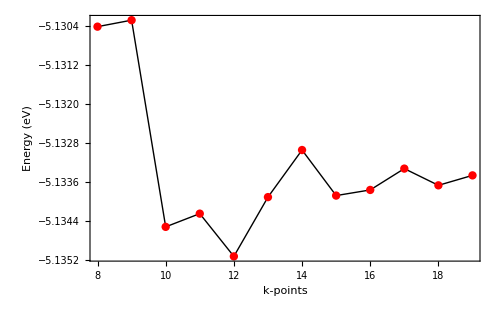

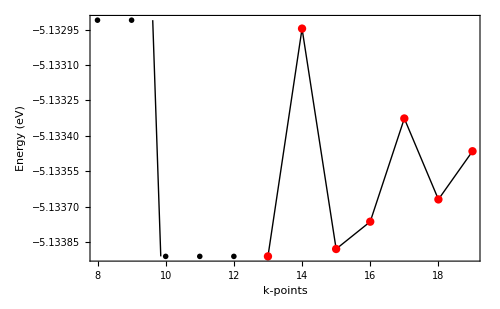

```mathematica
datakpt=Import["/home/edwin/wrk/DFT/part6/results/kps.dat","Table"][[All,{1,2}]]//Map[#/{1,2}&,#]&(*Number of atoms /2*)
{datakpt}//ListLinePlot[#,
Mesh->Full,PlotMarkers->{Automatic, 0}, Frame->True,PlotTheme->"Scientific",PlotRange->All,
Axes->None,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},FrameStyle->Black,
FrameLabel->{"k-points","Energy (eV)"}, ImageSize->500,
PlotStyle->{{Black,Thick},{Black,Thick}},Epilog->{Red,AbsolutePointSize[6],Point[datakpt]}]&
{datakpt}//ListLinePlot[#,
Mesh->Full,PlotMarkers->{Automatic, 0}, Frame->True,PlotTheme->"Scientific",PlotRange->{-5.133909945,-5.133909945+10^-3},
Axes->None,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},FrameStyle->Black,
FrameLabel->{"k-points","Energy (eV)"}, ImageSize->500,
PlotStyle->{{Black,Thick},{Black,Thick}},Epilog->{ Red,AbsolutePointSize[6],Point[datakpt]}]&
```

### EOS

5.29063+7169.82/x^2+31.9578/x^(4/3)-230.369/x^(2/3)

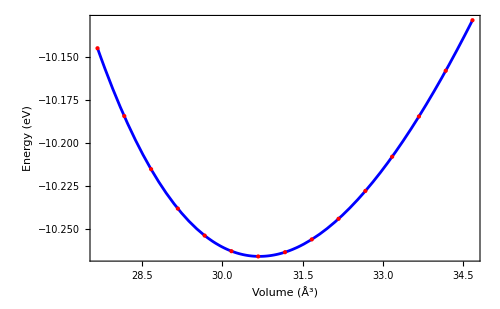

```mathematica
datacell=Import["/home/edwin/wrk/DFT/part6/results/cell.dat","Table"];
volData=(datacell[[1;;-1,1;;2]]//Transpose)//Transpose;(*0.25*)
EqState=c1+c2 x^-2+c3 x^(-4/3)+c4 x^(-2/3);
FitEqState=EqState/.FindFit[volData,EqState,{c1,c2,c3,c4},x ]
Vol=volData//Transpose//#[[1]]&;
Plot[FitEqState ,{x, Vol//Min, Vol//Max}, 
Frame->True,
PlotStyle->{Blue,Thick,AbsoluteThickness[2]}, Epilog->{PointSize[Large],Red,volData//Map[Point[#]&,#]&}, FrameLabel->{"Volume  (Å^3)", "Energy  (eV)"},ImageSize->500,FrameStyle->Black,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
Axes->None,PlotTheme->"Scientific"]
```

```mathematica
VolOptim=FindMinimum[FitEqState,{x,30.0}]
```

{-10.2659,{x→30.6907}}

```mathematica
<<Units`
x D[FitEqState,{x,2}]/.VolOptim[[2]]//Convert[# ElectronVolt/(10^-10 Meter)^3,Giga Pascal]&
(x/0.25)^(1/3)/.VolOptim[[2]]
```

107.51 Giga Pascal

4.96999

### DOS

9.06471

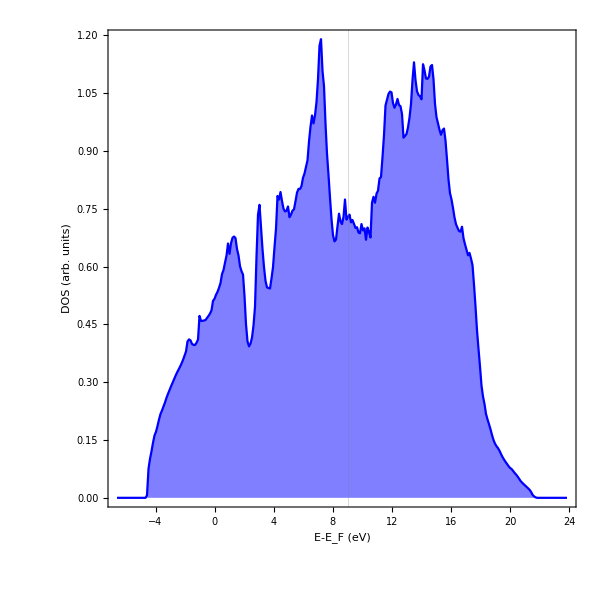

```mathematica
datados=Import["/home/edwin/wrk/DFT/part6/results/DOSCAR-bulk","Table"][[7;;7+300]][[All,{1,2}]];
efer=Import["/home/edwin/wrk/DFT/part6/results/DOSCAR-bulk","Table"][[6,4]]
ListPlot[datados,
Joined->True,
Frame->True,
Axes->False,
GridLines->{{efer},None},
FrameLabel->{"StyleBox[\"E\",FontSlant->\"Italic\"]-E_F (eV)", "DOS (arb. units)"},
BaseStyle->{"Helvetica",FontSize->15},
Filling->Axis, 
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->Blue,
AspectRatio->1,
ImageSize->600,
PlotRange->{All,All}
]
```

### Cohesive Energy

```mathematica
Ebul = -3.23023847;
Eatom=-0.06298736;
Eco=Ebul-Eatom
```

-3.16725

```mathematica
eossym141[x_]:=5.290634298312135+7169.821894451813/x^2+31.957795398743507/x^(4/3)-230.36909471874262/x^(2/3)+10.84223059;
eosfcc[x_]:=13.593859411480553+2113.9121339913554/x^2+3088.544117280115/x^(4/3)-565.2571081308844/x^(2/3)+10.84223059;
```

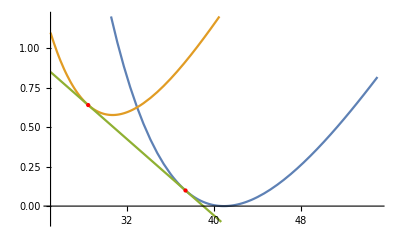

```mathematica
Plot[{eosfcc[x],eossym141[x],eql[x]},{x,25,55},PlotRange->{-0.1,1.2}, Epilog->{PointSize[Large],Red,Point[puntos]}]
```

```mathematica
NSolve[D]
```

```mathematica
sol=FindRoot[{D[eossym141[v2],v2]==D[eosfcc[v1],v1]==(eossym141[v2]-eosfcc[v1])/(v2-v1)},{{v1,38},{v2,26}}]
```

{v1→37.3853,v2→28.4555}

```mathematica
m=D[eossym141[v2],v2]/.sol
```

-0.0605342

```mathematica
y-y1=m(x-x1)
y=m(x-x1)+y1
```

```mathematica
eosfcc[v1]/.sol
```

0.0988083

```mathematica
eql[x_]:=-0.06053419136589022(x-28.455538064265028)+0.639362811107631
```

```mathematica
Solve[eql[x]==eosfcc[x],x]
```

{{x→37.3853}}

```mathematica
data=Table[{i,RandomReal[i]},{i,10}]
```

{{1,0.710281},{2,1.58935},{3,2.3658},{4,3.73079},{5,0.787152},{6,5.52654},{7,0.0336459},{8,5.87829},{9,1.72997},{10,6.40157}}

```mathematica
puntos={{37.38527719442725,0.09880827375490497},{28.455538064265028,0.639362811107631}}
```

{{37.3853,0.0988083},{28.4555,0.639363}}

```mathematica
<<Units`
0.06053419136589022//Convert[# ElectronVolt/(10^-10 Meter)^3,Giga Pascal]&
```

9.69865 Giga Pascal

## Part IX. The Nickel Oxide

13.2764+21434./x^2+354.246/x^(4/3)-605.254/x^(2/3)

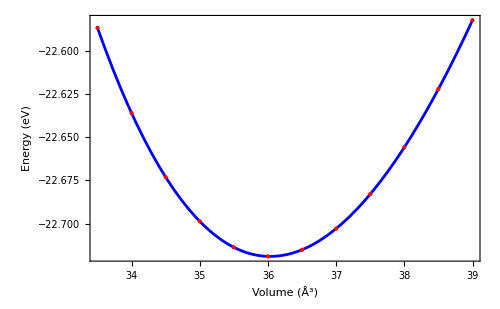

{-22.7189,{x→36.0319}}

207.524 Giga Pascal

5.24303

```mathematica
datacell=Import["/home/edwin/wrk/DFT/part7_nio/data/cell-nm.dat","Table"];
volData=(datacell[[1;;-1,1;;2]]//Transpose)//Transpose;(*0.25*)
EqState=c1+c2 x^-2+c3 x^(-4/3)+c4 x^(-2/3);
FitEqState=EqState/.FindFit[volData,EqState,{c1,c2,c3,c4},x ]
Vol=volData//Transpose//#[[1]]&;
Plot[FitEqState ,{x, Vol//Min, Vol//Max}, 
Frame->True,
PlotStyle->{Blue,Thick,AbsoluteThickness[2]}, Epilog->{PointSize[Large],Red,volData//Map[Point[#]&,#]&}, FrameLabel->{"Volume  (Å^3)", "Energy  (eV)"},ImageSize->500,FrameStyle->Black,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
Axes->None,PlotTheme->"Scientific"]
VolOptim=FindMinimum[FitEqState,{x,38.0}]
<<Units`
x D[FitEqState,{x,2}]/.VolOptim[[2]]//Convert[# ElectronVolt/(10^-10 Meter)^3,Giga Pascal]&
(x/0.25)^(1/3)/.VolOptim[[2]]
```

13.1309+9267.96/x^2+2752.27/x^(4/3)-721.705/x^(2/3)

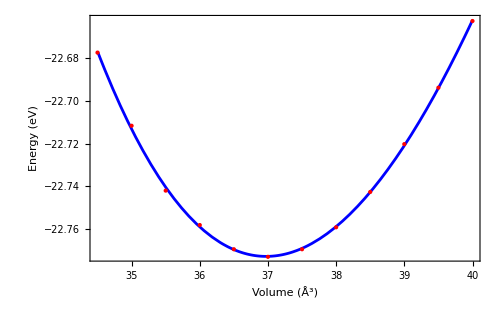

{-22.7728,{x→36.9735}}

164.409 Giga Pascal

5.28831

```mathematica
datacell=Import["/home/edwin/wrk/DFT/part7_nio/data/cell-fm.dat","Table"];
volData=(datacell[[1;;-1,1;;2]]//Transpose)//Transpose;(*0.25*)
EqState=c1+c2 x^-2+c3 x^(-4/3)+c4 x^(-2/3);
FitEqState=EqState/.FindFit[volData,EqState,{c1,c2,c3,c4},x ]
Vol=volData//Transpose//#[[1]]&;
Plot[FitEqState ,{x, Vol//Min, Vol//Max}, 
Frame->True,
PlotStyle->{Blue,Thick,AbsoluteThickness[2]}, Epilog->{PointSize[Large],Red,volData//Map[Point[#]&,#]&}, FrameLabel->{"Volume  (Å^3)", "Energy  (eV)"},ImageSize->500,FrameStyle->Black,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
Axes->None,PlotTheme->"Scientific"]
VolOptim=FindMinimum[FitEqState,{x,38.0}]
<<Units`
x D[FitEqState,{x,2}]/.VolOptim[[2]]//Convert[# ElectronVolt/(10^-10 Meter)^3,Giga Pascal]&
(x/0.25)^(1/3)/.VolOptim[[2]]
```

12.1879+19877.3/x^2+741.836/x^(4/3)-621.967/x^(2/3)

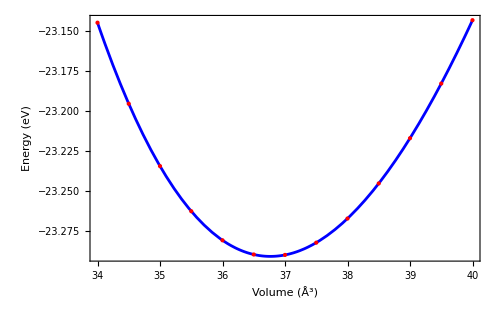

{-23.2909,{x→36.7655}}

194.394 Giga Pascal

5.27838

```mathematica
datacell=Import["/home/edwin/wrk/DFT/part7_nio/data/cell-afm.dat","Table"];
volData=(datacell[[1;;-1,1;;2]]//Transpose)//Transpose;(*0.25*)
EqState=c1+c2 x^-2+c3 x^(-4/3)+c4 x^(-2/3);
FitEqState=EqState/.FindFit[volData,EqState,{c1,c2,c3,c4},x ]
Vol=volData//Transpose//#[[1]]&;
Plot[FitEqState ,{x, Vol//Min, Vol//Max}, 
Frame->True,
PlotStyle->{Blue,Thick,AbsoluteThickness[2]}, Epilog->{PointSize[Large],Red,volData//Map[Point[#]&,#]&}, FrameLabel->{"Volume  (Å^3)", "Energy  (eV)"},ImageSize->500,FrameStyle->Black,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},
Axes->None,PlotTheme->"Scientific"]
VolOptim=FindMinimum[FitEqState,{x,38.0}]
<<Units`
x D[FitEqState,{x,2}]/.VolOptim[[2]]//Convert[# ElectronVolt/(10^-10 Meter)^3,Giga Pascal]&
(x/0.25)^(1/3)/.VolOptim[[2]]
```

7.96942

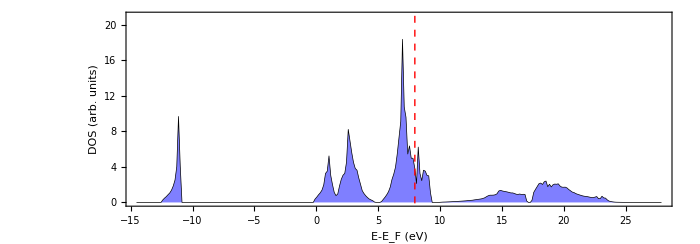

```mathematica
datados=Import["/home/edwin/wrk/DFT/part7_nio/data/DOSCAR-nm","Table"][[7;;7+300]][[All,{1,2}]];
efer=Import["/home/edwin/wrk/DFT/part7_nio/data/DOSCAR-nm","Table"][[6,4]]
ListPlot[datados,
Joined->True,
Frame->True,
Axes->False,
GridLines->{{efer},None},
GridLinesStyle->Directive[Red, Dashed,AbsoluteThickness[1]],
FrameLabel->{"StyleBox[\"E\",FontSlant->\"Italic\"]-E_F (eV)", "DOS (arb. units)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->20},
Filling->Axis, 
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
AspectRatio->0.35,
ImageSize->700,
PlotRange->{All,{0,21}}
]
```

7.65339

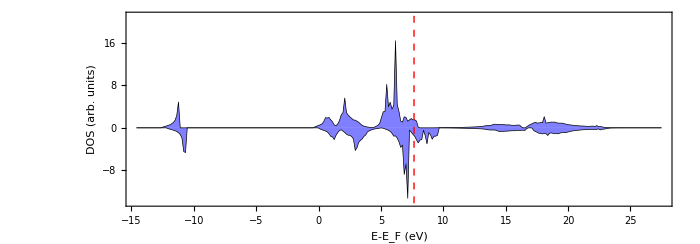

```mathematica
datadosfm=Import["/home/edwin/wrk/DFT/part7_nio/data/DOSCAR-fm","Table"];
dosfmUP=datadosfm[[7;;7+300]][[All,{1,2}]];
dosfmDWN=datadosfm[[7;;7+300]][[All,{1,3}]]//Map[#{1,-1}&,#]&;
efer=datadosfm[[6,4]]
ListPlot[{dosfmUP,dosfmDWN},
Joined->True,
Frame->True,
Axes->False,
GridLines->{{efer},None},
GridLinesStyle->Directive[Red, Dashed,AbsoluteThickness[1]],
FrameLabel->{"StyleBox[\"E\",FontSlant->\"Italic\"]-E_F (eV)", "DOS (arb. units)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->20},
Filling->Axis, 
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{{AbsoluteThickness[0.5],Black},{AbsoluteThickness[0.5],Black}},
AspectRatio->0.35,
ImageSize->700,
PlotRange->{All,{-14,21}}
]
```

7.31181

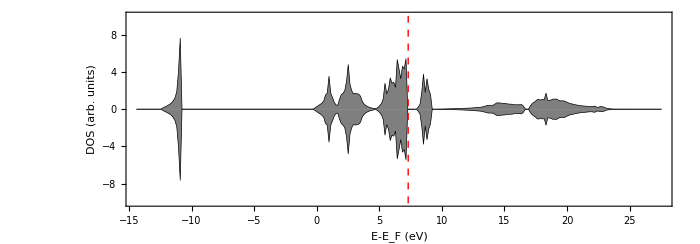

```mathematica
datadosafm=Import["/home/edwin/wrk/DFT/part7_nio/data/DOSCAR-afm","Table"];
dosafmUP=datadosafm[[7;;7+300]][[All,{1,2}]];
dosafmDWN=datadosafm[[7;;7+300]][[All,{1,3}]]//Map[#{1,-1}&,#]&;
efer=datadosafm[[6,4]]
ListPlot[{dosafmUP,dosafmDWN},
Joined->True,
Frame->True,
Axes->False,
GridLines->{{efer},None},
GridLinesStyle->Directive[Red, Dashed,AbsoluteThickness[1]],
FrameLabel->{"StyleBox[\"E\",FontSlant->\"Italic\"]-E_F (eV)", "DOS (arb. units)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->20},
Filling->Axis, 
FillingStyle->Directive[Opacity[0.5],Black],
PlotStyle->{{AbsoluteThickness[0.5],Black},{AbsoluteThickness[0.5],Black}},
AspectRatio->0.35,
ImageSize->700,
PlotRange->{All,{-10,10}}
]
```

7.31181

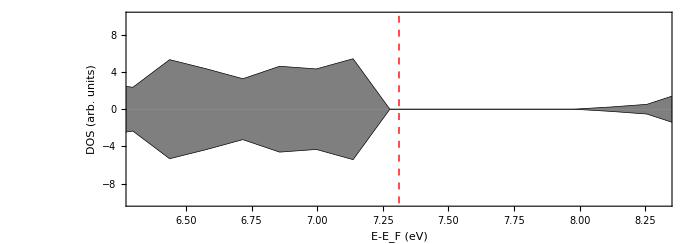

```mathematica
datadosafm=Import["/home/edwin/wrk/DFT/part7_nio/data/DOSCAR-afm","Table"];
dosafmUP=datadosafm[[7;;7+300]][[All,{1,2}]];
dosafmDWN=datadosafm[[7;;7+300]][[All,{1,3}]]//Map[#{1,-1}&,#]&;
efer=datadosafm[[6,4]]
ListPlot[{dosafmUP,dosafmDWN},
Joined->True,
Frame->True,
Axes->False,
GridLines->{{efer},None},
GridLinesStyle->Directive[Red, Dashed,AbsoluteThickness[1]],
FrameLabel->{"StyleBox[\"E\",FontSlant->\"Italic\"]-E_F (eV)", "DOS (arb. units)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->20},
Filling->Axis, 
FillingStyle->Directive[Opacity[0.5],Black],
PlotStyle->{{AbsoluteThickness[0.5],Black},{AbsoluteThickness[0.5],Black}},
AspectRatio->0.35,
ImageSize->700,
PlotRange->{{efer-1,efer+1},{-10,10}}
]
```

```mathematica
{{7.987783023631287,0.10375099760574713}}
```

```mathematica
efer-7.987783023631287
```

-0.675978

## Part X. The (100) Silicon Surface

```mathematica
datva=Import["/home/edwin/wrk/DFT/part8_si100/vacuum.dat","Table"]//Map[#/{1,5}&,#]&
```

{{5.,-4.64391},{6.,-4.64507},{7.,-4.63804},{8.,-4.63696},{9.,-4.63678},{10.,-4.63674},{11.,-4.6367},{12.,-4.63668},{13.,-4.63668},{14.,-4.63667},{15.,-4.63659}}

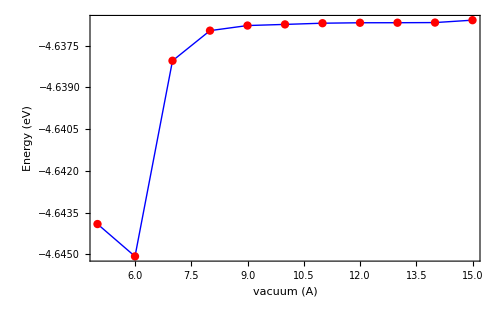

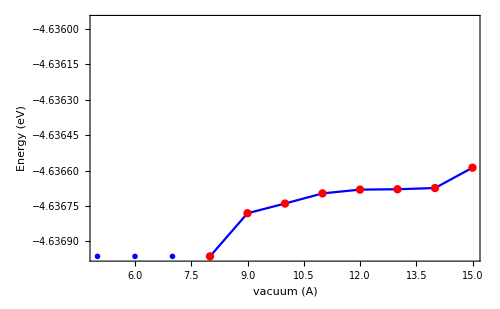

```mathematica
{datva}//ListLinePlot[#,
Mesh->Full,PlotMarkers->{Automatic,0}, Frame->True,PlotTheme->"Scientific",
Axes->None,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},FrameStyle->Black,
FrameLabel->{"vacuum (A)","Energy (eV)"}, ImageSize->500,PlotRange->All,
PlotStyle->{{Blue,Thick},{Blue,Thick}},Epilog->{Red,AbsolutePointSize[6],Point[datva]}]&
{datva}//ListLinePlot[#,
Mesh->Full,PlotMarkers->{Automatic,0}, Frame->True,PlotTheme->"Scientific",
Axes->None,BaseStyle->{FontSize->18,FontFamily->"Helvetica"},FrameStyle->Black,
FrameLabel->{"vacuum (A)","Energy (eV)"}, ImageSize->500,PlotRange->{-4.63696304,-4.63596304},
PlotStyle->{Blue,Thick},Epilog->{Red,AbsolutePointSize[6],Point[datva]}]&
```

-0.578687

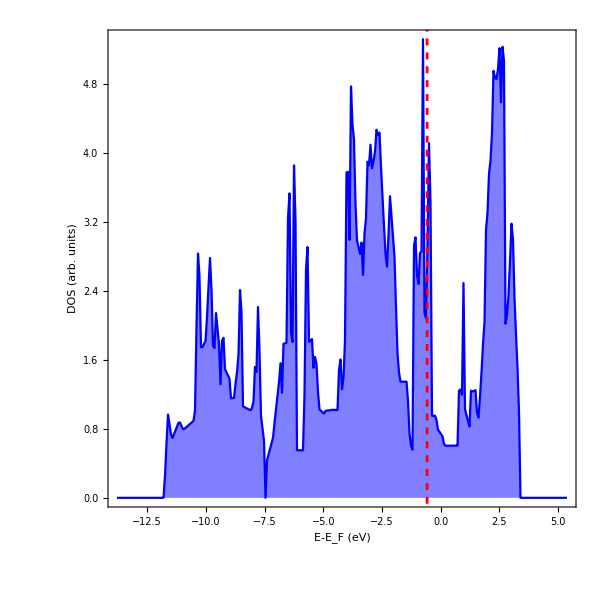

```mathematica
datados=Import["/home/edwin/wrk/DFT/part8_si100/DOSCAR-1x1l5v10.st","Table"][[7;;7+300]][[All,{1,2}]];
efer=Import["/home/edwin/wrk/DFT/part8_si100/DOSCAR-1x1l5v10.st","Table"][[6,4]]
ListPlot[datados,
Joined->True,
Frame->True,
Axes->False,
GridLines->{{efer},None},
GridLinesStyle->Directive[Red,Dashed,AbsoluteThickness[2]],
FrameLabel->{"StyleBox[\"E\",FontSlant->\"Italic\"]-E_F (eV)", "DOS (arb. units)"},
BaseStyle->{"Helvetica",FontSize->15},
Filling->Axis, 
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->Blue,
AspectRatio->1,
ImageSize->600,
PlotRange->{All,All}
]
```

-0.363995

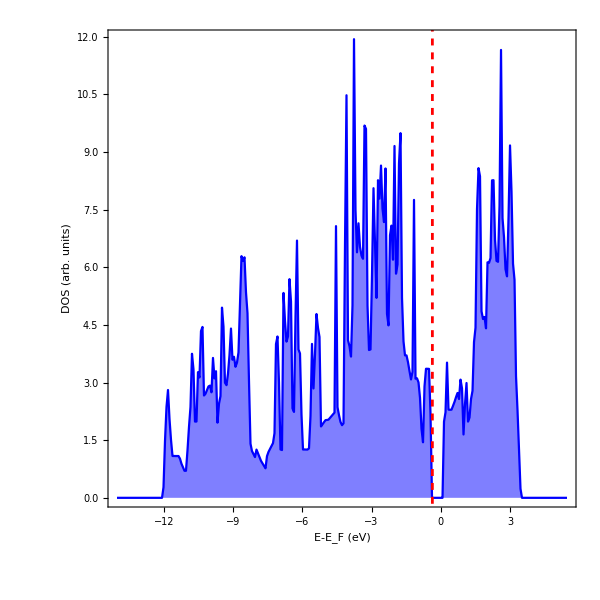

```mathematica
datados=Import["/home/edwin/wrk/DFT/part8_si100/DOSCAR-1x2l5v10c.st","Table"][[7;;7+300]][[All,{1,2}]];
efer=Import["/home/edwin/wrk/DFT/part8_si100/DOSCAR-1x2l5v10c.st","Table"][[6,4]]
ListPlot[datados,
Joined->True,
Frame->True,
Axes->False,
GridLines->{{efer},None},
GridLinesStyle->Directive[Red,Dashed,AbsoluteThickness[2]],
FrameLabel->{"StyleBox[\"E\",FontSlant->\"Italic\"]-E_F (eV)", "DOS (arb. units)"},
BaseStyle->{"Helvetica",FontSize->15},
Filling->Axis, 
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->Blue,
AspectRatio->1,
ImageSize->600,
PlotRange->{All,All}
]
```

-0.580947

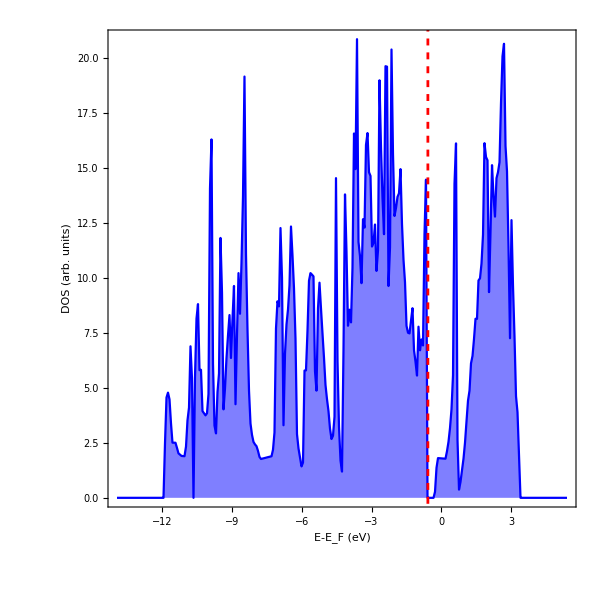

```mathematica
datados=Import["/home/edwin/wrk/DFT/part8_si100/DOSCAR-2x2l5v10.st","Table"][[7;;7+300]][[All,{1,2}]];
efer=Import["/home/edwin/wrk/DFT/part8_si100/DOSCAR-2x2l5v10.st","Table"][[6,4]]
ListPlot[datados,
Joined->True,
Frame->True,
Axes->False,
GridLines->{{efer},None},
GridLinesStyle->Directive[Red,Dashed,AbsoluteThickness[2]],
FrameLabel->{"StyleBox[\"E\",FontSlant->\"Italic\"]-E_F (eV)", "DOS (arb. units)"},
BaseStyle->{"Helvetica",FontSize->15},
Filling->Axis, 
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->Blue,
AspectRatio->1,
ImageSize->600,
PlotRange->{All,All}
]
```

```mathematica
res = Import["/home/edwin/wrk/DFT/part8_si100/surface.dat"][[All,{1,2}]]
res[[1]]/{1,7}//TableForm
res[[2;;4]]//Map[#/{1,14}&,#]&//TableForm
res[[-1]]/{1,28}//TableForm
```

{{1x1l5v10,-31.3677},{1x2l5v10,-62.7345},{1x2l5v10b,-64.2107},{1x2l5v10c,-64.3838},{2x2l5v10,-128.909}}

1x1l5v10
-4.48111

1x2l5v10 | -4.48104
1x2l5v10b | -4.58648
1x2l5v10c | -4.59884

2x2l5v10
-4.60389

-0.580947

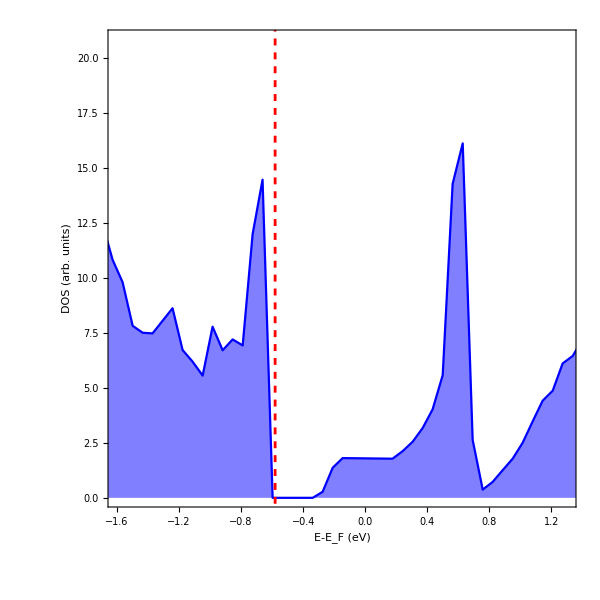

```mathematica
datados=Import["/home/edwin/wrk/DFT/part8_si100/DOSCAR-2x2l5v10.st","Table"][[7;;7+300]][[All,{1,2}]];
efer=Import["/home/edwin/wrk/DFT/part8_si100/DOSCAR-2x2l5v10.st","Table"][[6,4]]
ListPlot[datados,
Joined->True,
Frame->True,
Axes->False,
GridLines->{{efer},None},
GridLinesStyle->Directive[Red,Dashed,AbsoluteThickness[2]],
FrameLabel->{"StyleBox[\"E\",FontSlant->\"Italic\"]-E_F (eV)", "DOS (arb. units)"},
BaseStyle->{"Helvetica",FontSize->15},
Filling->Axis, 
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->Blue,
AspectRatio->1,
ImageSize->600,
PlotRange->{{-1.6,1.3},All}
]
```

```mathematica
Import["/home/edwin/wrk/DFT/part8_si100/PARCHG-2x2l5v10.png"]
```

-Graphics-

```mathematica
in=Import["/home/edwin/wrk/DFT/part8_si100/PARCHG-2x2l5v10.vasp","Table"];
```

```mathematica
numat = Plus@@in[[7]]
thelattice=in[[3;;5]]
stm=(in[[7+numat+3+1;;-1]]//Flatten)
```

28

{{7.733,0.,0.},{0.,7.733,0.},{0.,0.,16.4681}}

{0.50813,0.53791,0.62398,0.7587,0.9331,1.1397,1.3736,1.6309,1.906,2.1891,2.4663,2.7231,2.9493,3.1424,3.3051,3.4398,3.5444,3.6121,3.6357,725722,3.0408,3.0552,3.0408,2.9991,2.9335,2.8458,2.7337,2.5922,2.4176,2.2115,1.9824,1.7426,1.5041,1.2758,1.0635,0.87218,0.70806,0.57948,0.49556}
 |  |  |  |

```mathematica
stm[[-1]]
```

0.49556

```mathematica
divX=in[[7+numat+3,1]]
divY=in[[7+numat+3,2]]
```

72

72

```mathematica
zrange=in[[5,{2,3}]]
```

{0.,16.4681}

```mathematica
transformDATA=(#//Partition[#,divX]&//Partition[#,divY]&//
Map[Append[#,First[#]]&,#,{2}]&//
Map[Append[#,First[#]]&,#]&//Transpose[#,{3,2,1}]&)&;
```

```mathematica
stm1=stm//transformDATA;
```

```mathematica
theInterpola=ListInterpolation[#,{{0,in[[3,1]]},{0,in[[4,2]]},{0,in[[5,3]]}},PeriodicInterpolation->{True,True,False}]&;
```

```mathematica
stminterpolation=stm1//theInterpola
```

InterpolatingFunction[{{…, 0., 7.733, …}, {…, 0., 7.733, …}, {0., 16.4681}}, <>]

```mathematica
stminterpolation[1.9,2.6,8.6]
```

19.9326

```mathematica
nx=2;
ny=2;
ContourPlot3D[stminterpolation[x,y,z]==0.08,
{x,0,nx thelattice[[1,1]]},
{y,0,ny thelattice[[2,2]]},
{z,8.6,11.6},
(*ColorFunction->Function[{x,y,z,f},Glow[ColorData["Aquamarine"][z]]],*)
PlotPoints->20,
MaxRecursion->0,
BoxRatios->{1, ny thelattice[[2,2]]/(nx thelattice[[1,1]]), (11.6-8.6)/(nx thelattice[[1,1]])},
ViewPoint->{0, 0, ∞},
BaseStyle->{"Helvetica",FontSize->13},
ContourStyle->Directive[Opacity[1.]],
(*Lighting->None,*)
Mesh->None
]
```

-Graphics3D-

```mathematica
(*10 A away the top most atom
in our case is 2 A tengo que revisar l CONTCARfile*)
```

```mathematica
nx=2;
ny=2;
ContourPlot3D[stminterpolation[x,y,z]==0.08,
{x,0,nx thelattice[[1,1]]},
{y,0,ny thelattice[[2,2]]},
{z,8.6,11.6},
(*ColorFunction->Function[{x,y,z,f},Glow[ColorData["ColorData["Aquamarine"]"][z]]],*)
ColorFunction->"BlueGreenYellow",
PlotPoints->60,
MaxRecursion->0,
BoxRatios->{1, ny thelattice[[2,2]]/(nx thelattice[[1,1]]), (11.6-8.6)/(nx thelattice[[1,1]])},
ViewPoint->{0, 0, ∞},
BaseStyle->{"Helvetica",FontSize->13},
ContourStyle->Directive[Opacity[1.]],
(*Lighting->None,*)
Mesh->None
]
```

-Graphics3D-